```mathematica
hoop =ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}];
colors={RGBColor[0.394, 0.394, 0.394],RGBColor[0.668, 0.668, 0.668],RGBColor[0.177, 0.177, 0.177]};
```

```mathematica
x0=Pi/2;
vx0=0;
y0=0;
vy0=1;

tf=15;

sol=NDSolve[{x''[t]==Sin[y[t]-x[t]],y''[t]==-Sin[y[t]-x[t]],x'[0]==vx0,y'[0]==vy0,x[0]==x0,y[0]==y0},{x,y},{t,0,tf}];

s1= x  /. First@sol;
s2= y /. First@sol;

Animate[Show[hoop,ListLinePlot[{{Cos[s1[t]],Sin[s1[t]]},{Cos[s2[t]],Sin[s2[t]]}},PlotStyle->{Thickness[.008],Black}],Graphics[{colors[[1]],PointSize[.1],Point[{Cos[s1[t]],Sin[s1[t]]}]}],Graphics[{colors[[2]],PointSize[.1],Point[{Cos[s2[t]],Sin[s2[t]]}]}]],{t,0,tf}]
```

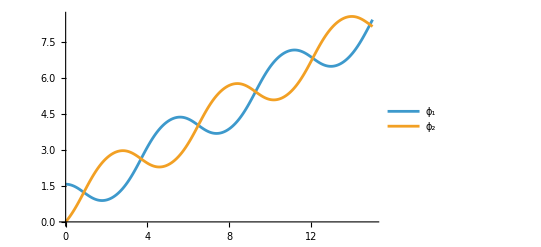

```mathematica
Show[ListLinePlot[{Legended[s1,Style["ϕ_1",12]],Legended[s2,Style["ϕ_2",12]]},PlotRange->All]]
```

Extensions/special cases

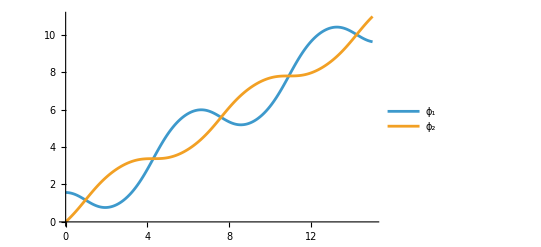

```mathematica
α=2;

sol1=NDSolve[{x''[t]==Sin[y[t]-x[t]],y''[t]==- Sin[y[t]-x[t]]/α,x'[0]==vx0,y'[0]==vy0,x[0]==x0,y[0]==y0},{x,y},{t,0,tf}];

s11= x  /. First@sol1;
s21= y /. First@sol1;

Animate[Show[hoop,ListLinePlot[{{Cos[s11[t]],Sin[s11[t]]},{Cos[s21[t]],Sin[s21[t]]}},PlotStyle->{Thickness[.008],Black}],Graphics[{colors[[1]],PointSize[.1],Point[{Cos[s11[t]],Sin[s11[t]]}]}],Graphics[{colors[[2]],PointSize[.1],Point[{Cos[s21[t]],Sin[s21[t]]}]}]],{t,0,tf}]
Show[ListLinePlot[{Legended[s11,Style["ϕ_1",12]],Legended[s21,Style["ϕ_2",12]]},PlotRange->All]]
```

Three Masses, Two Springs

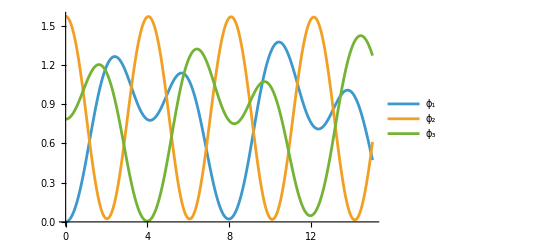

```mathematica
x0=0;
vx0=0;
y0=Pi/2;
vy0=0;
z0=Pi/4;
vz0=0;

tf=15;

sol=NDSolve[{x''[t]==Sin[y[t]-x[t]],y''[t]==-Sin[y[t]-x[t]]-Sin[y[t]-z[t]],z''[t]==Sin[y[t]-z[t]],x'[0]==vx0,y'[0]==vy0,z'[0]==vz0,x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,tf}];

s1= x  /. First@sol;
s2= y /. First@sol;
s3= z/. First@sol;

Animate[Show[hoop,ListLinePlot[{{Cos[s1[t]],Sin[s1[t]]},{Cos[s2[t]],Sin[s2[t]]}},PlotStyle->{Thickness[.008],Black}],ListLinePlot[{{Cos[s2[t]],Sin[s2[t]]},{Cos[s3[t]],Sin[s3[t]]}},PlotStyle->{Thickness[.008],Black}],Graphics[{colors[[1]],PointSize[.08],Point[{Cos[s1[t]],Sin[s1[t]]}]}],Graphics[{colors[[2]],PointSize[.08],Point[{Cos[s2[t]],Sin[s2[t]]}]}],Graphics[{colors[[3]],PointSize[.08],Point[{Cos[s3[t]],Sin[s3[t]]}]}]],{t,0,tf}]
Show[ListLinePlot[{Legended[s1,Style["ϕ_1",12]],Legended[s2,Style["ϕ_2",12]],Legended[s3,Style["ϕ_3",12]]},PlotRange->All]]
```